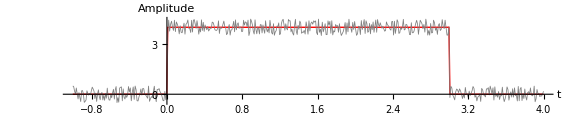

```mathematica
a = 4;
t1 = 0;
t2 = 3;
c =0;
d = 5;
b = 0.5;

g[t_]:=Piecewise[{{a,t1<=t<=t2}},0];
u[t_]:=g[t]+b RandomReal[{-1,1}]+c Sin[d t]

Plot[{g[t], u[t]},{t,-1,4},
 Exclusions->None,
 AspectRatio->0.2, 
PlotStyle->{{Red,Thick},{Gray,Thickness[0.001]}}, 
PlotPoints->9,
 AxesLabel->{t, "Amplitude"},
 PlotLegends->Placed[{"Original signal", "Noisy signal"},Right], 
ImageSize->Large
]
```

```mathematica
fourierFilter[u_,{t_,tmin_,tmax_},sampleRate_,v0_]:=Module[{timeValues,signalValues,fftValues,freqRange,freqStep,freqValues,filteredFFT,filteredSignal},timeValues=Subdivide[tmin,tmax,(tmax-tmin)*sampleRate-1];
signalValues=u/@timeValues;
fftValues=Fourier[signalValues,FourierParameters->{-1,1}];
freqRange=Length[fftValues];
freqStep=sampleRate/freqRange;
freqValues=Table[(n-1)*sampleRate/freqRange,{n,freqRange}];
freqValues=If[#>sampleRate/2,#-sampleRate,#]&/@freqValues;
filteredFFT=MapThread[If[Abs[#2]<=v0,#1,0]&,{fftValues,freqValues}];
filteredSignal=InverseFourier[filteredFFT,FourierParameters->{-1,1}];
{timeValues,Re[filteredSignal]}]

{times,filtered}=fourierFilter[u,{t,-1,4},100,5];

Manipulate[{times,filtered}=fourierFilter[u,{t,-1,4},100,v0];
ListLinePlot[{Transpose[{times,g/@times}],Transpose[{times,u/@times}],Transpose[{times,filtered}]  },AspectRatio->0.2,PlotStyle->{{Red,Thickness[0.005]},{Gray,Thickness[0.001]},{Blue,Thickness[0.003]} },PlotLegends->Placed[{"Original","Noisy",StringTemplate["Filtered (|f|≤`` Hz)"][v0]},Right],ImageSize->800,PlotLabel->StringTemplate["Частотная фильтрация (v0 = `` Hz)"][v0],AxesLabel->{"Time","Amplitude"}],{{v0,1,"Частотный порог v0 (Hz)"},0.1,50,0.1,Appearance->"Labeled"},TrackedSymbols:>{v0}]


animation=Table[{times,filtered}=fourierFilter[u,{t,-1,4},100,v0];
ListLinePlot[{Transpose[{times,g/@times}],Transpose[{times,u/@times}],Transpose[{times,filtered}]},PlotStyle->{{Red,Thickness[0.005]},{Gray,Thickness[0.001]},{Blue,Thickness[0.003]}},PlotLegends->Placed[{"Original","Noisy",StringTemplate["Filtered (|f|≤`` Hz)"][v0]},Right],ImageSize->800,PlotLabel->StringTemplate["Частотная фильтрация (v0 = `` Hz)"][v0],AxesLabel->{"Time","Amplitude"},AspectRatio->0.2,PlotRange->{{-1,4},{-1,5}} ],{v0,0,20,0.2} ];

ListAnimate[animation,AnimationRate->20,DisplayAllSteps->True];
```